```mathematica
A = {{1,-1,0,-3,0},{-2,5,0,0,0},{0,0,4,6,4},{-4,0,2,7,0},{0,8,0,0,-5}};
```

```mathematica
b = {0.1,0.2,0.3,0.4,0.5};
```

```mathematica
x=Inverse[A].b
```

{-0.0813988,0.00744048,0.257515,-0.0629464,-0.0880952}

```mathematica
A.%
```

{0.1,0.2,0.3,0.4,0.5}

```mathematica
A //MatrixForm
```

```mathematica
({{1, -1, 0, -3, 0}, {-2, 5, 0, 0, 0}, {0, 0, 4, 6, 4}, {-4, 0, 2, 7, 0}, {0, 8, 0, 0, -5}})
```

```mathematica
As = {{1,-2,0,-4,0},{-2,5,0,0,8},{0,0,4,2,0},{-4,0,2,7,0},{0,8,0,0,-5}};
```

```mathematica
As//MatrixForm
```

(1 | -2 | 0 | -4 | 0
-2 | 5 | 0 | 0 | 8
0 | 0 | 4 | 2 | 0
-4 | 0 | 2 | 7 | 0
0 | 8 | 0 | 0 | -5)

```mathematica
Inverse[As] . b
```

{-0.200396,0.0336634,0.120965,-0.0919307,-0.0461386}

```mathematica
Eigenvalues[As]
```

{Root10.3Root[-4040-1567 #1+1132 #1^2-74 #1^3-12 #1^4+#1^5&,5]10.33873849664362,Root-9.53Root[-4040-1567 #1+1132 #1^2-74 #1^3-12 #1^4+#1^5&,1]-9.534114699624665,Root8.94Root[-4040-1567 #1+1132 #1^2-74 #1^3-12 #1^4+#1^5&,4]8.942570079451391,Root3.55Root[-4040-1567 #1+1132 #1^2-74 #1^3-12 #1^4+#1^5&,3]3.545495438195968,Root-1.29Root[-4040-1567 #1+1132 #1^2-74 #1^3-12 #1^4+#1^5&,2]-1.2926893146663134}

```mathematica
PositiveDefiniteMatrixQ[As]
```

False

```mathematica
SymmetricMatrixQ[As]
```

True

```mathematica
PDA = {{2,1,0,0,0},{1,2,1,0,0},{0,1,2,1,0},{0,0,1,2,1},{0,0,0,1,2}};
PDA // MatrixForm
```

(2 | 1 | 0 | 0 | 0
1 | 2 | 1 | 0 | 0
0 | 1 | 2 | 1 | 0
0 | 0 | 1 | 2 | 1
0 | 0 | 0 | 1 | 2)

```mathematica
PositiveDefiniteMatrixQ[PDA]
```

True

```mathematica
ex = {0.2,0.4,0.6,0.8,1.0};
```

```mathematica
PDA . ex
```

{0.8,1.6,2.4,3.2,2.8}

```mathematica
PDAL = {{2,0,0,0,0},{1,2,0,0,0},{0,1,2,0,0},{0,0,1,2,0},{0,0,0,1,2}};
PDAL // MatrixForm
```

(2 | 0 | 0 | 0 | 0
1 | 2 | 0 | 0 | 0
0 | 1 | 2 | 0 | 0
0 | 0 | 1 | 2 | 0
0 | 0 | 0 | 1 | 2)

```mathematica
PDAL . ex
```

{0.4,1.,1.6,2.2,2.8}

```mathematica
B = DiagonalMatrix[Table[0.0014427,10]]
```

{{0.0014427,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0014427,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.0014427,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.0014427,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.0014427,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.0014427,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.0014427,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.0014427,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0014427,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0014427}}

```mathematica
B[[8,6]]=0.03022;B[[6,8]]=0.03022;B[[9,6]]=0.02022;B[[6,9]]=0.02022; 
B[[6,6]]=0.2932; B[[9,9]]=0.0028167;
```

```mathematica
B//MatrixForm
```

(0.0014427 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0014427 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0014427 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.0014427 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.0014427 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.2932 | 0. | 0.03022 | 0.02022 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0014427 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.03022 | 0. | 0.0014427 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.02022 | 0. | 0. | 0.0028167 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0014427)

```mathematica
PositiveSemidefiniteMatrixQ[B]
```

False

```mathematica
SymmetricMatrixQ[B]
```

True

```mathematica
rhs = B . c
```

{0.00014427,0.00028854,0.00043281,0.00057708,0.00072135,0.218294,0.00100989,0.0192862,0.014667,0.0014427}

```mathematica
c = {0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0};
```

```mathematica
Inverse[B].c
```

{69.3145,138.629,207.943,277.258,346.572,46.6389,485.201,-422.421,-15.2796,693.145}

```mathematica
B.%
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

# Testing MatrixMarket

```mathematica
bcsstk01=Import["/Users/toniivas/Documents/CODE/TestMatrixSolver/TestMatrixSolver/DATA/bcsstk01.mtx"]
```

SparseArray[…]

```mathematica
PositiveDefiniteMatrixQ[bcsstk01]
```

True

```mathematica
bk01 = Table[i/48, {i,1,48}] // N
```

{0.0208333,0.0416667,0.0625,0.0833333,0.104167,0.125,0.145833,0.166667,0.1875,0.208333,0.229167,0.25,0.270833,0.291667,0.3125,0.333333,0.354167,0.375,0.395833,0.416667,0.4375,0.458333,0.479167,0.5,0.520833,0.541667,0.5625,0.583333,0.604167,0.625,0.645833,0.666667,0.6875,0.708333,0.729167,0.75,0.770833,0.791667,0.8125,0.833333,0.854167,0.875,0.895833,0.916667,0.9375,0.958333,0.979167,1.}

```mathematica
xk01 = bcsstk01.bk01
```

{830949.,2.07752×10^6,-3.23951×10^6,2.25042×10^8,3.17167×10^8,5.84125×10^8,1.38595×10^6,3.25357×10^6,-3.33649×10^6,3.13375×10^8,3.83139×10^8,7.06847×10^8,950438.,-122014.,-3.42253×10^6,1.39018×10^9,8.4169×10^8,7.55304×10^8,4.99428×10^6,-5.84211×10^6,-1.1297×10^6,6.89542×10^8,6.17417×10^8,9.47125×10^8,1.69508×10^6,-1.47431×10^6,-333727.,1.23745×10^9,4.8524×10^8,3.24948×10^8,-2.3327×10^6,1.64868×10^7,-5.03327×10^6,1.37411×10^9,1.48059×10^9,2.37918×10^9,-2.18235×10^6,-4.60421×10^6,5.58998×10^6,1.76172×10^9,1.68936×10^9,2.55804×10^9,2.86205×10^6,-4.62253×10^6,3.28024×10^6,2.99123×10^9,1.10635×10^9,4.56993×10^8}

```mathematica
bcsstk05=Import["/Users/toniivas/Documents/CODE/TestMatrixSolver/TestMatrixSolver/DATA/bcsstk05.mtx"]
```

SparseArray[…]

```mathematica
PositiveDefiniteMatrixQ[bcsstk05]
```

True

Solve the bcsstk05 example:

```mathematica
bk05=Table[i/153,{i,153}];
```

```mathematica
LinearSolve[bcsstk05,bk05]
```

{0.000980422,0.0000336135,0.00103956,0.000891189,-0.00010306,0.000927529,0.000894749,-0.0000363424,0.000938312,0.000894478,0.0000303272,0.000945681,0.000890378,0.000174935,0.000960043,0.000886567,0.000103464,0.00094586,0.00088725,0.0000366754,0.000938503,0.000832473,-0.000036304,0.000872959,0.000836401,0.0000300739,0.000879337,0.000828822,0.000102948,0.000879748,0.000824787,0.0000364821,0.000872301,0.000771936,-0.000116433,0.000799553,0.0007734,-0.0000358761,0.000805234,0.000772831,0.0000296257,0.00081198,0.000767645,0.000226215,0.000838565,0.000764318,0.000101623,0.000812043,0.000766606,0.0000361184,0.000805853,0.000711258,-0.0000340126,0.000740238,0.000713016,0.0000289245,0.000742505,0.000709227,0.0000980786,0.000747321,0.000700206,0.0000353492,0.000737408,0.000652077,-0.0000809667,0.000670653,0.000652292,-0.0000302056,0.000672669,0.000652476,0.0000278894,0.000679365,0.000647434,0.000186653,0.000699996,0.000643688,0.0000917062,0.000678638,0.000646829,0.0000342363,0.000673351,0.00057431,-0.0000446589,0.000583041,0.000567372,0.0000259006,0.000585187,0.000570549,0.000102023,0.000596482,0.000557104,0.0000331797,0.000580613,0.000491992,-0.0000551275,0.000497557,0.000490947,0.0000240941,0.000504659,0.000484438,0.000110225,0.000505766,0.000484494,0.0000336805,0.000488331,0.000422105,-0.0000625379,0.000407935,0.000415079,0.0000215353,0.000421357,0.000416936,0.000111184,0.000431819,0.000405612,0.000030698,0.000413975,0.000340693,-0.000062476,0.000331032,0.000333341,0.0000181538,0.000332726,0.000335243,0.000106058,0.000344513,0.000322958,0.0000301437,0.000306607,0.000268522,-0.0000578315,0.000245446,0.000263314,0.0000145578,0.000258592,0.000260112,0.0000931802,0.000265042,0.000253145,0.0000226629,0.000247571,0.000126147,-0.0000366563,0.00013273,0.000117674,7.68976×10^-6,0.000112608,0.000124278,0.0000544115,0.000125132,0.000111379,9.96099×10^-6,0.000119043}

```mathematica
bcsstk04=Import["/Users/toniivas/Documents/CODE/TestMatrixSolver/TestMatrixSolver/DATA/bcsstk04.mtx"]
```

SparseArray[…]

```mathematica
bk04 = Table[i/132,{i,1,132}];
```

```mathematica
LinearSolve[bcsstk04,bk04]
```

{0.110005,0.117495,-0.0165123,-0.000124323,0.000115669,-3.27587×10^-6,0.111462,0.114283,0.00046047,-0.000110234,0.000108514,-6.3962×10^-6,0.116565,0.119054,0.000971522,-0.00011583,0.000113093,-2.59793×10^-6,0.114982,0.11274,0.0178921,-0.000118502,0.000121498,-3.85904×10^-6,0.108476,0.115361,-0.0101344,0.0000351528,-0.0000330086,-5.37302×10^-6,0.108954,0.111292,0.00113623,0.0000350312,-0.0000338377,5.58084×10^-6,0.113371,0.115902,0.00160882,0.0000358561,-0.0000348605,-0.0000158952,0.112741,0.110689,0.0127624,0.0000337957,-0.0000335504,-5.59504×10^-6,0.103649,0.109677,-0.00595634,3.53056×10^-7,-2.09127×10^-7,-4.94033×10^-6,0.103285,0.105748,0.00168774,4.99125×10^-7,-6.89285×10^-7,-3.08184×10^-6,0.107525,0.109315,0.0020916,9.38093×10^-7,1.83037×10^-7,-7.13866×10^-6,0.107759,0.105991,0.00984606,1.22796×10^-6,-3.45917×10^-7,-5.16789×10^-6,0.102364,0.107499,-0.00259237,6.76703×10^-6,-6.07422×10^-6,-5.19846×10^-6,0.102759,0.104511,0.00218119,7.35948×10^-6,-8.53626×10^-7,-4.15665×10^-6,0.106014,0.10794,0.00254469,1.61881×10^-6,-6.75995×10^-6,-5.78273×10^-6,0.105499,0.104014,0.00735155,3.88259×10^-6,-3.32673×10^-6,-5.3545×10^-6,0.104122,0.105963,0.0348567,8.12286×10^-6,-6.03061×10^-6,-5.08904×10^-6,0.100524,0.104681,-0.00184352,0.0000167648,-0.0000154887,-4.50069×10^-6,0.0997053,0.101196,0.00243668,0.0000150863,1.08921×10^-6,-5.58485×10^-6,0.102405,0.103862,0.00273205,-2.56549×10^-7,-0.0000141199,-4.4923×10^-6,0.103346,0.102141,0.0072541,-6.9667×10^-6,8.22387×10^-6,-4.71308×10^-6,0.102136,0.103611,0.0347522,0.0000106017,-8.2844×10^-6,-5.26985×10^-6}

```mathematica
PositiveDefiniteMatrixQ[bcsstk04]
```

True

```mathematica
Max[bcsstk05]
```

3.29908×10^6

```mathematica
matLT = Import["/Users/toniivas/Documents/CODE/TestMatrixSolver/TestMatrixSolver/DATA/mat_10_LT.mtx"]
```

SparseArray[…]

```mathematica
lt = Table[i/10,{i,1,10}]
```

{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

```mathematica
rhs = matLT.lt
```

{0.00014427,0.00028854,0.00043281,0.00057708,0.00072135,0.218294,0.00100989,0.0192862,0.014667,0.0014427}

```mathematica
s =LinearSolve[matLT,lt]
```

{69.3145,138.629,207.943,277.258,346.572,46.6389,485.201,-422.421,-15.2796,693.145}

Test solution:

```mathematica
matLT.s == lt
```

True

Export for test :

```mathematica
Export["/Users/toniivas/Documents/CODE/TestMatrixSolver/TestMatrixSolver/DATA/mat_10_row.mtx",matLT,"MTX"]
```

/Users/toniivas/Documents/CODE/TestMatrixSolver/TestMatrixSolver/DATA/mat_10_row.mtx

```mathematica
matLT//MatrixForm
```

(0.0014427 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0014427 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0014427 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.0014427 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.0014427 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.2932 | 0. | 0.03022 | 0.02022 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0014427 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.03022 | 0. | 0.0014427 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.02022 | 0. | 0. | 0.0028167 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0014427)

```mathematica
matLT//InputForm
```

SparseArray[Automatic, {10, 10}, 0., {1, {{0, 1, 2, 3, 4, 5, 8, 9, 11, 13, 14}, {{1}, {2}, {3}, {4}, {5}, {6}, {8}, {9}, 
   {7}, {6}, {8}, {6}, {9}, {10}}}, {0.0014427, 0.0014427, 0.0014427, 0.0014427, 0.0014427, 0.2932, 0.03022, 0.02022, 
  0.0014427, 0.03022, 0.0014427, 0.02022, 0.0028167, 0.0014427}}]

```mathematica
s1 = LinearSolve[matLT,lt]
```

{69.3145,138.629,207.943,277.258,346.572,2.04638,485.201,511.651,304.833,693.145}

Test pardiso:

```mathematica
pardiso = Import["/Users/toniivas/Documents/CODE/TestMatrixSolver/TestMatrixSolver/DATA/pardisoc.mtx"];
pard = Table[1./8,{i,1,8}];
sp = LinearSolve[pardiso,pard]
```

{-0.00523253,-0.000426641,0.0146563,-0.0140799,0.00302153,-0.0134542,0.02484,0.0237979}

```mathematica
pardiso//MatrixForm
```

(7. | 0. | 1. | 0. | 0. | 2. | 7. | 0.
0. | -4. | 8. | 0. | 2. | 0. | 0. | 0.
1. | 8. | 1. | 0. | 0. | 0. | 0. | 5.
0. | 0. | 0. | 7. | 0. | 0. | 9. | 0.
0. | 2. | 0. | 0. | 5. | -1. | 5. | 0.
2. | 0. | 0. | 0. | 1. | 0. | 0. | 5.
7. | 0. | 0. | 9. | 5. | 0. | 11. | 0.
0. | 0. | 5. | 0. | 0. | 5. | 0. | 5.)

```mathematica
Export["/Users/toniivas/Documents/CODE/TestMatrixSolver/TestMatrixSolver/DATA/pardisomex.mtx",pardiso,"MTX"]
```

/Users/toniivas/Documents/CODE/TestMatrixSolver/TestMatrixSolver/DATA/pardisomex.mtx

```mathematica
trPar // MatrixForm
```

(7. | 0. | 1. | 0. | 0. | 2. | 7. | 0.
0. | -4. | 8. | 0. | 2. | 0. | 0. | 0.
1. | 8. | 1. | 0. | 0. | 0. | 0. | 5.
0. | 0. | 0. | 7. | 0. | 0. | 9. | 0.
0. | 2. | 0. | 0. | 5. | -1. | 5. | 0.
2. | 0. | 0. | 0. | -1. | 0. | 0. | 5.
7. | 0. | 0. | 9. | 5. | 0. | 11. | 0.
0. | 0. | 5. | 0. | 0. | 5. | 0. | 5.)

Test solution :

```mathematica
pardiso . sp == pard
```

True

```mathematica
pardiso . sp
```

{1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
xsol = {-0.041860,-0.003413,0.117250,-0.112640,0.024172,-0.107633,0.198720,0.190383}
```

{-0.04186,-0.003413,0.11725,-0.11264,0.024172,-0.107633,0.19872,0.190383}

```mathematica
pardiso.xsol
```

{1.,0.999996,1.,1.,1.21527,0.844023,1.,1.}

```mathematica
PositiveDefiniteMatrixQ[pardiso]
```

False

```mathematica
pda = Import["/Users/toniivas/Documents/CODE/TestMatrixSolver/TestMatrixSolver/DATA/PDA.mtx"];
```

```mathematica
pd = Table[i/5,{i,1,5}];
sd = LinearSolve[pda,pd]
```

{0.1,1.11022×10^-16,0.3,1.11022×10^-16,0.5}

Test solution:

```mathematica
pda . sd == pd
```

True

```mathematica
pda//MatrixForm
```

(2. | 1. | 0. | 0. | 0.
1. | 2. | 1. | 0. | 0.
0. | 1. | 2. | 1. | 0.
0. | 0. | 1. | 2. | 1.
0. | 0. | 0. | 1. | 2.)

```mathematica
M = SparseArray[{Band[{1,1}]->4,Band[{2,1}]->-1,Band[{1,2}]->-1,Band[{1,6}]->-1,Band[{6,1}]->-1},{25,25}];
```

```mathematica
M[[1,1]]=9; M[[2,2]]=5; M[[3,3]]=8; M[[1,3]]=-4; M[[3,1]]=-4; M[[5,6]]=0; M[[6,5]]=0;
M[[10,11]]=0;M[[11,10]]=0; M[[15,16]]=0; M[[16,15]]=0; M[[20,21]]=0;M[[21,20]]=0;
M//MatrixForm
```

(9 | -1 | -4 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 5 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4 | -1 | 8 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 4 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 4 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 4)

```mathematica
v = {3,2,1,1,2,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,2,1,1,1,2};
Length[v]
```

25

```mathematica
Inverse[M].v //N
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
v//MatrixForm
```

(3
2
1
1
2
1
0
0
0
1
1
0
0
0
1
1
0
0
0
1
2
1
1
1
2)

```mathematica
Mi = SparseArray[{Band[{1,1}]->4,Band[{2,1}]->-1,Band[{1,2}]->-1,Band[{1,6}]->-1,Band[{6,1}]->-1},{25,25}];
PositiveDefiniteMatrixQ[Mi]
```

True

```mathematica
LinearSolve[Mi,v]//N
```

{1.90587,1.99358,1.75476,1.85641,2.3421,2.62992,2.31369,2.16905,2.32879,2.88208,2.95801,2.46219,2.27896,2.40761,2.89943,2.85785,2.29811,2.077,2.12326,2.45016,2.27585,1.79541,1.60767,1.55826,1.5021}

```mathematica
mtxExport = ExportString[M,"MTX"];
```

```mathematica
mtxExport
```

%%MatrixMarket matrix coordinate integer symmetric
%Created with the Wolfram Language : www.wolfram.com
25 25 66
1 1 9
2 1 -1
2 2 5
3 3 8
3 2 -1
3 1 -4
4 4 4
4 3 -1
5 5 4
5 4 -1
6 6 4
6 1 -1
7 6 -1
7 2 -1
7 7 4
8 3 -1
8 8 4
8 7 -1
9 8 -1
9 9 4
9 4 -1
10 9 -1
10 5 -1
10 10 4
11 6 -1
11 11 4
12 7 -1
12 11 -1
12 12 4
13 13 4
13 12 -1
13 8 -1
14 9 -1
14 14 4
14 13 -1
15 10 -1
15 14 -1
15 15 4
16 11 -1
16 16 4
17 16 -1
17 12 -1
17 17 4
18 13 -1
18 17 -1
18 18 4
19 19 4
19 18 -1
19 14 -1
20 15 -1
20 19 -1
20 20 4
21 21 4
21 16 -1
22 21 -1
22 17 -1
22 22 4
23 18 -1
23 23 4
23 22 -1
24 24 4
24 23 -1
24 19 -1
25 20 -1
25 25 4
25 24 -1

```mathematica
Export["/Users/toniivas/Documents/CODE/Chaleur/C++/LIBAL/TESTING/TEST_SOLV/CG/VERSION_GLOBALE/DATA/matrixe.mtx",M, "MTX"]
```

/Users/toniivas/Documents/CODE/Chaleur/C++/LIBAL/TESTING/TEST_SOLV/CG/VERSION_GLOBALE/DATA/matrixe.mtx

```mathematica
reimport=Import["/Users/toniivas/Documents/CODE/Chaleur/C++/LIBAL/TESTING/TEST_SOLV/CG/VERSION_GLOBALE/DATA/matrixe.mtx"]
```

SparseArray[…]

```mathematica
reimport // MatrixForm
```

(9. | -1. | -4. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1. | 5. | -1. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-4. | -1. | 8. | -1. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -1. | 4. | -1. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -1. | 4. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1. | 0. | 0. | 0. | 0. | 4. | -1. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1. | 0. | 0. | 0. | -1. | 4. | -1. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -1. | 0. | 0. | 0. | -1. | 4. | -1. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -1. | 0. | 0. | 0. | -1. | 4. | -1. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | -1. | 4. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 4. | -1. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | -1. | 4. | -1. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | -1. | 4. | -1. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | -1. | 4. | -1. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | -1. | 4. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 4. | -1. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | -1. | 4. | -1. | 0. | 0. | 0. | -1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | -1. | 4. | -1. | 0. | 0. | 0. | -1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | -1. | 4. | -1. | 0. | 0. | 0. | -1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | -1. | 4. | 0. | 0. | 0. | 0. | -1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 4. | -1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | -1. | 4. | -1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | -1. | 4. | -1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | -1. | 4. | -1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | -1. | 4.)

```mathematica
SymmetricMatrixQ[reimport]
```

True

```mathematica
Import["/Users/toniivas/Documents/CODE/TestMatrixSolver/TestMatrixSolver/DATA/pardisoc.mtx"]
```

```mathematica
reimport // InputForm
```

SparseArray[Automatic, {25, 25}, 0., {1, {{0, 4, 8, 13, 17, 20, 24, 29, 34, 39, 43, 47, 52, 57, 62, 66, 70, 75, 80, 85, 
   89, 92, 96, 100, 104, 107}, {{1}, {2}, {3}, {6}, {1}, {2}, {3}, {7}, {3}, {2}, {1}, {4}, {8}, {4}, {3}, {5}, {9}, {5}, 
   {4}, {10}, {6}, {1}, {7}, {11}, {6}, {2}, {7}, {8}, {12}, {3}, {8}, {7}, {9}, {13}, {8}, {9}, {4}, {10}, {14}, {9}, 
   {5}, {10}, {15}, {6}, {11}, {12}, {16}, {7}, {11}, {12}, {13}, {17}, {13}, {12}, {8}, {14}, {18}, {9}, {14}, {13}, 
   {15}, {19}, {10}, {14}, {15}, {20}, {11}, {16}, {17}, {21}, {16}, {12}, {17}, {18}, {22}, {13}, {17}, {18}, {19}, 
   {23}, {19}, {18}, {14}, {20}, {24}, {15}, {19}, {20}, {25}, {21}, {16}, {22}, {21}, {17}, {22}, {23}, {18}, {23}, 
   {22}, {24}, {24}, {23}, {19}, {25}, {20}, {25}, {24}}}, {9., -1., -4., -1., -1., 5., -1., -1., 8., -1., -4., -1., -1., 
  4., -1., -1., -1., 4., -1., -1., 4., -1., -1., -1., -1., -1., 4., -1., -1., -1., 4., -1., -1., -1., -1., 4., -1., -1., 
  -1., -1., -1., 4., -1., -1., 4., -1., -1., -1., -1., 4., -1., -1., 4., -1., -1., -1., -1., -1., 4., -1., -1., -1., -1., 
  -1., 4., -1., -1., 4., -1., -1., -1., -1., 4., -1., -1., -1., -1., 4., -1., -1., 4., -1., -1., -1., -1., -1., -1., 4., 
  -1., 4., -1., -1., -1., -1., 4., -1., -1., 4., -1., -1., 4., -1., -1., -1., -1., 4., -1.}}]

```mathematica
re=Table[i/25,{i,1,25}];
LinearSolve[reimport,re]
```

{0.241475,0.287129,0.337718,0.422285,0.307845,0.495274,0.776454,0.906428,0.883579,0.609095,0.723167,1.13698,1.30796,1.23651,0.844957,0.820411,1.26035,1.43193,1.34953,0.934226,0.658124,0.972086,1.08987,1.03545,0.74242}

Solve Laplace problem:

```mathematica
lap=Import["/Users/toniivas/Documents/CODE/TestMatrixSolver/TestMatrixSolver/DATA/gr_30_30.mtx"]
```

SparseArray[…]

```mathematica
SymmetricMatrixQ[lap]
```

True

```mathematica
lapb=Table[i/900,{i,900}];
```

```mathematica
LinearSolve[lap,lapb]
```

{0.110149,0.215875,0.314571,0.405561,0.488648,0.563829,0.631196,0.690878,0.743021,0.787769,0.825256,0.855594,0.878873,0.895154,0.904467,0.906809,0.902144,0.8904,0.871469,0.845209,0.811443,0.76996,0.720518,0.662842,0.596632,0.521557,0.437265,0.343381,0.239505,0.125211,0.225859,0.438345,0.635855,0.817598,0.983373,1.13326,1.26749,1.38633,1.4901,1.57909,1.65358,1.71379,1.75992,1.79208,1.81034,1.81469,1.80506,1.78131,1.74322,1.69051,1.62281,1.53972,1.44074,1.32532,1.19286,1.04269,0.874116,0.686375,0.478674,0.250177,0.343764,0.664291,0.960843,1.23309,1.48106,1.70505,1.90546,2.08278,2.2375,2.37009,2.48097,2.57051,2.63898,2.68659,2.71342,2.71949,2.70467,2.66875,2.61142,2.53224,2.43068,2.30609,2.15775,1.98483,1.78641,1.56149,1.30901,1.02783,0.716772,0.374587,0.462433,0.891407,1.28693,1.64922,1.97871,2.27598,2.54171,2.77664,2.98146,3.15684,3.30339,3.42159,3.51185,3.57443,3.60947,3.61698,3.59682,3.54869,3.47217,3.36669,3.23152,3.06582,2.86858,2.6387,2.37494,2.07597,1.74035,1.36656,0.953016,0.498059,0.580908,1.11798,1.61189,2.06341,2.47342,2.8429,3.17285,3.46428,3.71816,3.93537,4.1167,4.2628,4.3742,4.45124,4.49412,4.50284,4.47725,4.41697,4.32148,4.19004,4.02176,3.81555,3.57016,3.28418,2.95606,2.58411,2.16651,1.70133,1.18658,0.62018,0.69843,1.34257,1.93371,2.47319,2.96238,3.40268,3.79546,4.14205,4.44372,4.70159,4.91667,5.08978,5.22158,5.31253,5.36285,5.37259,5.34155,5.2693,5.15518,4.99833,4.79764,4.55181,4.25931,3.91843,3.52728,3.08379,2.58576,2.03084,1.4166,0.740515,0.814326,1.56388,2.25055,2.87624,3.44283,3.95218,4.40607,4.80619,5.15413,5.45129,5.6989,5.898,6.04938,6.15361,6.21099,6.22158,6.18514,6.10118,5.96895,5.78742,5.55527,5.27097,4.93271,4.53845,4.08596,3.57278,2.99629,2.35372,1.64215,0.858603,0.927961,1.78066,2.56059,3.27023,3.91199,4.48822,5.00114,5.45285,5.84526,6.18009,6.45884,6.68275,6.85278,6.96961,7.03362,7.04489,7.00318,6.90793,6.75825,6.55295,6.29053,5.96919,5.58684,5.1411,4.62935,4.04874,3.39621,2.66852,1.86226,0.973952,1.03871,1.99167,2.86202,3.65281,4.36702,5.00752,5.577,6.07798,6.51277,6.88342,7.19169,7.43906,7.62667,7.75535,7.82555,7.83739,7.79059,7.68454,7.51823,7.29032,6.99907,6.64242,6.21797,5.723,5.15449,4.50916,3.78347,2.97368,2.07589,1.08604,1.14593,2.19566,3.15298,4.02156,4.80498,5.50665,6.12979,6.67738,7.15212,7.55642,7.89237,8.16167,8.36569,8.50537,8.58129,8.59357,8.54195,8.42573,8.24379,7.9946,7.67622,7.2863,6.82211,6.28057,5.65823,4.95134,4.15588,3.26756,2.28191,1.1943,1.24895,2.39131,3.43151,4.37393,5.22277,5.98202,6.65546,7.24656,7.75846,8.19397,8.55548,8.845,9.06408,9.21385,9.29496,9.30759,9.25147,9.12583,8.92942,8.66054,8.317,7.89618,7.39499,6.80994,6.13716,5.37239,4.51107,3.54834,2.47911,1.29813,1.34708,2.57721,3.69557,4.70723,5.61709,6.42978,7.14966,7.78073,8.32663,8.79055,9.17526,9.48305,9.71571,9.87453,9.96027,9.97318,9.91295,9.77876,9.56923,9.28247,8.91604,8.46702,7.93195,7.30693,6.5876,5.76916,4.84648,3.81407,2.66618,1.39685,1.43956,2.75187,3.94292,5.01855,5.9844,6.84579,7.60772,8.27476,8.85106,9.34026,9.74551,10.0694,10.314,10.4807,10.5705,10.5836,10.5197,10.378,10.1568,9.85425,9.46751,8.99337,8.42798,7.76699,7.00552,6.13822,5.1593,4.06261,2.84167,1.48976,1.52557,2.91366,4.17116,5.30475,6.32086,7.22559,8.02459,8.72308,9.32574,9.83671,10.2595,10.5971,10.8517,11.0251,11.1182,11.1315,11.0645,10.9163,10.6853,10.3693,9.9651,9.46929,8.87759,8.18515,7.38655,6.47581,5.44647,4.29162,3.00399,1.57604,1.6042,3.06081,4.37766,5.56238,6.62228,7.56427,8.39477,9.11964,9.74416,10.273,10.71,11.0586,11.3213,11.4999,11.5957,11.609,11.5395,11.3862,11.1473,10.8202,10.4019,9.88831,9.27477,8.55595,7.72584,6.77778,5.70457,4.49849,3.1514,1.6548,1.67448,3.19134,4.55951,5.78766,6.88405,7.85649,8.71221,9.45781,10.0992,10.6415,11.0891,11.4458,11.7143,11.8967,11.9943,12.0076,11.9362,11.7791,11.5344,11.1994,10.7704,10.2433,9.61294,8.8734,8.01806,7.03955,5.92985,4.68035,3.28193,1.72508,1.73528,3.30307,4.71349,5.97637,7.10106,8.09633,8.9703,9.73033,10.383,10.934,11.3882,11.7497,12.0216,12.2061,12.3047,12.3179,12.2455,12.0862,11.838,11.498,11.0624,10.5265,9.88484,9.13086,8.25729,7.256,6.11809,4.83395,3.3934,1.78574,1.78536,3.39353,4.83598,6.12383,7.26762,8.27722,9.16169,9.92921,10.5871,11.1415,11.598,11.9608,12.2334,12.4182,12.5169,12.53,12.4572,12.2973,12.0482,11.7067,11.2688,10.7294,10.0824,9.32096,8.43695,7.42144,6.26458,4.95567,3.48333,1.83556,1.82332,3.45994,4.92288,6.22473,7.37736,8.39183,9.27822,10.0456,10.702,11.2542,11.7081,12.0684,12.3389,12.5221,12.6198,12.6328,12.5605,12.4019,12.1546,11.8153,11.3797,10.8423,10.1968,9.4355,8.54964,7.52944,6.36398,5.04138,3.54891,1.87309,1.84754,3.49911,4.96955,6.27308,7.42309,8.43194,9.31082,10.0697,10.7173,11.2611,11.7073,12.0611,12.3264,12.506,12.6018,12.6144,12.5436,12.3881,12.1456,11.8124,11.3841,10.855,10.2181,9.4653,8.58708,7.57272,6.41022,5.08637,3.58692,1.89671,1.85613,3.50736,4.97061,6.26201,7.39664,8.38828,9.24929,9.99058,10.6216,11.1503,11.5835,11.9264,12.1833,12.3572,12.4498,12.4621,12.3937,12.2434,12.0086,11.6857,11.2701,10.7558,10.1353,9.40006,8.53985,7.543,6.39633,5.08519,3.59361,1.9045,1.84689,3.48037,4.91981,6.18357,7.28862,8.25029,9.08217,9.79608,10.4021,10.9088,11.3232,11.6507,11.8959,12.0617,12.1501,12.1619,12.0969,11.9538,11.7299,11.4218,11.0245,10.5318,9.93606,9.22817,8.39727,7.43076,6.31423,5.03147,3.56458,1.89422,1.81717,3.41298,4.80976,6.02847,7.08821,8.00596,8.79653,9.4726,10.0449,10.5222,10.9117,11.2193,11.4493,11.6047,11.6877,11.699,11.6383,11.5044,11.2948,11.0058,10.6326,10.1688,9.60659,8.93649,8.14709,7.22496,6.15446,4.91769,3.49458,1.86316,1.76373,3.29894,4.6316,5.7857,6.78274,7.64142,8.37768,9.00492,9.5342,9.97458,10.3333,10.6162,10.8275,10.9703,11.0466,11.0572,11.0018,10.8793,10.6872,10.4219,10.0786,9.65104,9.13143,8.51007,7.7752,6.91269,5.90575,4.73476,3.37722,1.80801,1.68251,3.13048,4.37443,5.442,6.35729,7.14065,7.80895,8.376,8.85298,9.24886,9.57077,9.82424,10.0134,10.1413,10.2097,10.2195,10.1704,10.0612,9.88965,9.65244,9.34492,8.96107,8.49326,7.93192,7.26525,6.47869,5.55457,4.47155,3.20451,1.72459,1.56819,2.89759,4.0246,4.98117,5.79407,6.48502,7.07134,7.5668,7.98224,8.32622,8.60544,8.82505,8.98887,9.09962,9.15899,9.16771,9.12563,9.03164,8.88372,8.67879,8.41261,8.07962,7.67267,7.18267,6.59818,5.90476,5.08427,4.11405,2.9662,1.60747,1.41356,2.58697,3.56447,4.38301,5.07171,5.65282,6.1433,6.55611,6.90123,7.18636,7.41746,7.59903,7.73444,7.82602,7.87525,7.88276,7.84841,7.77128,7.64962,7.48076,7.26104,6.98558,6.64805,6.24028,5.75178,5.16896,4.47414,3.6441,2.64858,1.44919,1.20806,2.17988,2.97051,3.62203,4.16444,4.61886,5.00049,5.32053,5.5874,5.80749,5.98565,6.12553,6.22984,6.30045,6.33852,6.34458,6.31852,6.25961,6.16644,6.03691,5.86808,5.65599,5.3955,5.07985,4.70022,4.24487,3.69795,3.0375,2.23236,1.23889,0.934758,1.64822,2.21028,2.66587,3.04148,3.35422,3.61577,3.8345,4.01653,4.16645,4.28772,4.3829,4.45389,4.502,4.52805,4.5324,4.51498,4.47527,4.41232,4.32464,4.21018,4.06616,3.88891,3.67361,3.41382,3.1008,2.72239,2.2608,1.68855,0.959076,0.562023,0.94543,1.23927,1.47435,1.66682,1.82639,1.95949,2.0706,2.16297,2.23899,2.30046,2.34871,2.38472,2.40917,2.42247,2.42481,2.41616,2.39625,2.36458,2.32041,2.26266,2.18991,2.10024,1.99114,1.85919,1.69973,1.50606,1.26808,0.96906,0.577086}

```mathematica
ms = SparseArray[{Band[{1,1}]->1,Band[{1,2}]-> 1/2, Band[{2,1}]-> 1/2},{9,9}];
```

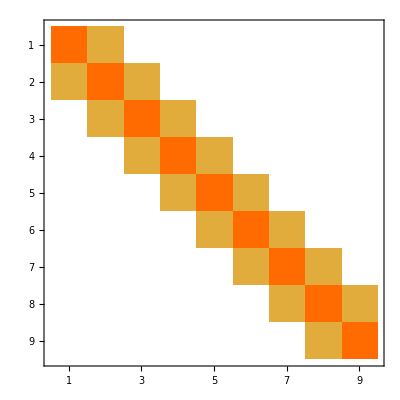

```mathematica
MatrixPlot[ms]
```

```mathematica
ms
```

SparseArray[…]

```mathematica
SymmetricMatrixQ[ms]
```

True

```mathematica
Export["matrixe.mtx",ms, "MTX"]
```

matrixe.mtx

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["matrixe.mtx"]]]
```

```mathematica
solms = Table[1.,{i,1,9}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
ms[[1,1]]=3.;rhs=ms.solms
```

{3.5,2.,2.,2.,2.,2.,2.,2.,1.5}

```mathematica
ms//MatrixForm
```

(2. | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Inverse[ms].rhs
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
ExportString[, "MTX"]
```

%%MatrixMarket matrix coordinate real symmetric\r
%Created with the Wolfram Language : www.wolfram.com\r
9 9 17\r
1 1    1.0000000000000000E+00\r
2 1    5.0000000000000000E-01\r
2 2    1.0000000000000000E+00\r
3 2    5.0000000000000000E-01\r
3 3    1.0000000000000000E+00\r
4 3    5.0000000000000000E-01\r
4 4    1.0000000000000000E+00\r
5 4    5.0000000000000000E-01\r
5 5    1.0000000000000000E+00\r
6 5    5.0000000000000000E-01\r
6 6    1.0000000000000000E+00\r
7 6    5.0000000000000000E-01\r
7 7    1.0000000000000000E+00\r
8 7    5.0000000000000000E-01\r
8 8    1.0000000000000000E+00\r
9 8    5.0000000000000000E-01\r
9 9    1.0000000000000000E+00\r